# Henry Osei Lab2 9/19/2019 Math 274-002

## Experiment 14.1 14.1(a)

```mathematica
Clear[f,a,b];
```

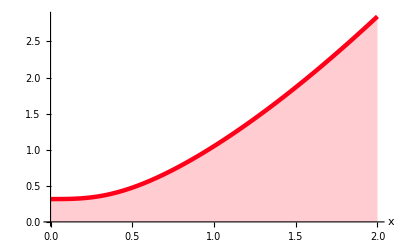

```mathematica
f[x_]:=Sqrt[x^3+0.1]; a=0; b=2;
Plot[f[x],{x,a,b},Filling->Bottom,AxesLabel->{"x",""},
		                PlotStyle->{{RGBColor[1,0,.1],Thickness[.008]}}]
```

## 14.1 (B)

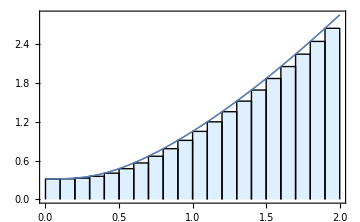

```mathematica
plotLeftSum[f_,a_,b_,n_]:=Module[{h,p1,p2},
h:=(b-a)/n;
p1=Plot[f[x],{x,a,b},PlotStyle->Thick,PlotRange->All,Frame->True,Axes->False,ImageSize->Medium];
p2=Graphics[{{LightBlue,Table[Polygon[{{x,0},{x+h,0},{x+h,f[x]},{x,f[x]}}],{x,a,b-h,h}]},Table[Line[{{x,0},{x,f[x]},{x+h,f[x]},{x+h,0}}],{x,a,b-h,h}]}];
Show[p1,p2,p1]]
plotLeftSum[f,0,2,20]
```

```mathematica
leftSum[f_,a_,b_,n_,k_]:=N[ Sum[f[a+i*(b-a)/n]*(b-a)/n, {i,0,n-1} ],k]
```

```mathematica
leftSum[f,0,2,10,10]
```

2.1931

```mathematica
showLeftSums[f_,a_,b_,n_,k_]:=Module[{g,i},
g[x_]=f[x];
Manipulate[Column[{plotLeftSum[g,a,b,i],"Left Riemann sum:",leftSum[g,a,b,i,k]}],{{i,1,"n"},1,n,1}]]
```

```mathematica
showLeftSums[f,0,2,40,10]
```

```mathematica
plotRightSum[f_,a_,b_,n_]:=Module[{h,p1,p2},
h:=(b-a)/n;
p1=Plot[f[x],{x,a,b},PlotStyle->Thick,PlotRange->All,Frame->True,Axes->False,ImageSize->Medium];
p2=Graphics[{
{LightBlue,Table[Polygon[{{x,0},{x+h,0},{x+h,f[x+h]},{x,f[x+h]}}],{x,a,b-h,h}]},Table[Line[{{x,0},{x,f[x+h]},{x+h,f[x+h]},{x+h,0}}],{x,a,b-h,h}]}];
Show[p1,p2,p1]]
```

## 14.1 (B)

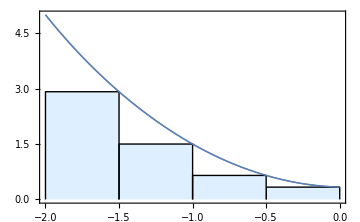

```mathematica
Clear[f]
f[x_]:=((x^2)+1/(x+3))
plotRightSum[f,-2,0,4]
```

```mathematica
rightSum[f_,a_,b_,n_,k_]:=N[ Sum[f[a+i*(b-a)/n]*(b-a)/n, {i,1,n} ],k]
```

```mathematica
rightSum[f,0,2,4,8]
```

4.2289683

```mathematica
showRightSums[f_,a_,b_,n_,k_]:=Module[{g,i},
g[x_]=f[x];
Manipulate[Column[{plotRightSum[g,a,b,i],"Right Riemann sum:",rightSum[g,a,b,i,k]}],{{i,1,"n"},1,n,1}]]
```

## 14.1 (c)

```mathematica
showRightSums[f,0,2,40,10]
```

### 14.2 (2a)

```mathematica
Clear[f,a,b];
```

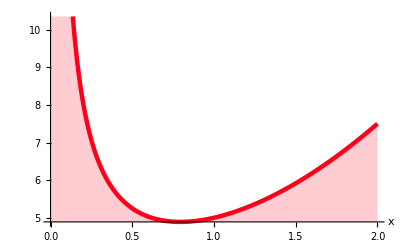

```mathematica
f[x_]:=(x^2)+1/x+3; a=0; b=2;
Plot[f[x],{x,a,b},Filling->Bottom,AxesLabel->{"x",""},
		                PlotStyle->{{RGBColor[1,0,.1],Thickness[.008]}}]
```

## 14.2 (2 b)

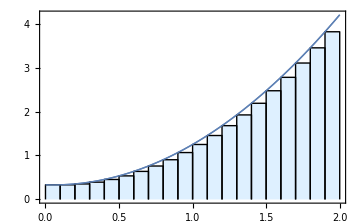

```mathematica
plotLeftSum[f_,a_,b_,n_]:=Module[{h,p1,p2},
h:=(b-a)/n;
p1=Plot[f[x],{x,a,b},PlotStyle->Thick,PlotRange->All,Frame->True,Axes->False,ImageSize->Medium];
p2=Graphics[{{LightBlue,Table[Polygon[{{x,0},{x+h,0},{x+h,f[x]},{x,f[x]}}],{x,a,b-h,h}]},Table[Line[{{x,0},{x,f[x]},{x+h,f[x]},{x+h,0}}],{x,a,b-h,h}]}];
Show[p1,p2,p1]]
plotLeftSum[f,0,2,20]
```

```mathematica
leftSum[f_,a_,b_,n_,k_]:=N[ Sum[f[a+i*(b-a)/n]*(b-a)/n, {i,0,n-1} ],k]
```

```mathematica
leftSum[f,0,2,10,10]
```

2.804395851

```mathematica
plotRightSum[f_,a_,b_,n_]:=Module[{h,p1,p2},
h:=(b-a)/n;
p1=Plot[f[x],{x,a,b},PlotStyle->Thick,PlotRange->All,Frame->True,Axes->False,ImageSize->Medium];
p2=Graphics[{
{LightBlue,Table[Polygon[{{x,0},{x+h,0},{x+h,f[x+h]},{x,f[x+h]}}],{x,a,b-h,h}]},Table[Line[{{x,0},{x,f[x+h]},{x+h,f[x+h]},{x+h,0}}],{x,a,b-h,h}]}];
Show[p1,p2,p1]]
```

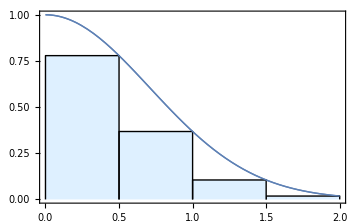

```mathematica
Clear[f]
f[x_]:=E^(-x^2)
plotRightSum[f,0,2,4]
```

```mathematica
rightSum[f_,a_,b_,n_,k_]:=N[ Sum[f[a+i*(b-a)/n]*(b-a)/n, {i,1,n} ],k]
```

```mathematica
rightSum[f,0,2,4,8]
```

0.63519754

```mathematica
showRightSums[f_,a_,b_,n_,k_]:=Module[{g,i},
g[x_]=f[x];
Manipulate[Column[{plotRightSum[g,a,b,i],"Right Riemann sum:",rightSum[g,a,b,i,k]}],{{i,1,"n"},1,n,1}]]
```

```mathematica
showRightSums[f,0,2,40,10]
```

## 14.3 (2A)

```mathematica
Clear[f,a,b];
```

```mathematica
g[x_]:=Sin[x]/(x^2)+1; a=0; b=2;
```

```mathematica
showRiemannSums[f_,a_,b_,n_,k_]:=Module[{g,i,j,h,p1,p2,ξ,η}, 
g[x_]=f[x];
p1=Plot[g[x],{x,a,b},PlotStyle->Thick,PlotRange->All,Frame->True,Axes->False,ImageSize->Medium];
Manipulate[h:=(b-a)/i;ξ=Table[RandomInteger[10]/10,{i}];η=Table[a+j*h,{j,1,i}];
p2=Graphics[{{LightBlue,Table[Polygon[{{η[[j]]-h,0},{η[[j]],0},{η[[j]],g[η[[j]]-ξ[[j]]*h]},{η[[j]]-h,g[η[[j]]-ξ[[j]]*h]}}],{j,1,i}]},Table[Line[{{η[[j]]-h,0},{η[[j]]-h,g[η[[j]]-ξ[[j]]*h]},{η[[j]],g[η[[j]]-ξ[[j]]*h]},{η[[j]],0},{η[[j]]-h,0}}],{j,1,i}],{PointSize->0.015,Blue,Table[Point[{η[[j]]-ξ[[j]]*h,0}],{j,1,i}]}}];Column[{Show[p1,p2,p1],"Riemann sum:",N[Sum[g[η[[j]]-ξ[[j]]*h]*h, {j,1,i} ],k]}],
{{i,1,"n"},1,n,1}]]
showRiemannSums[f,0,2,10,10]
```